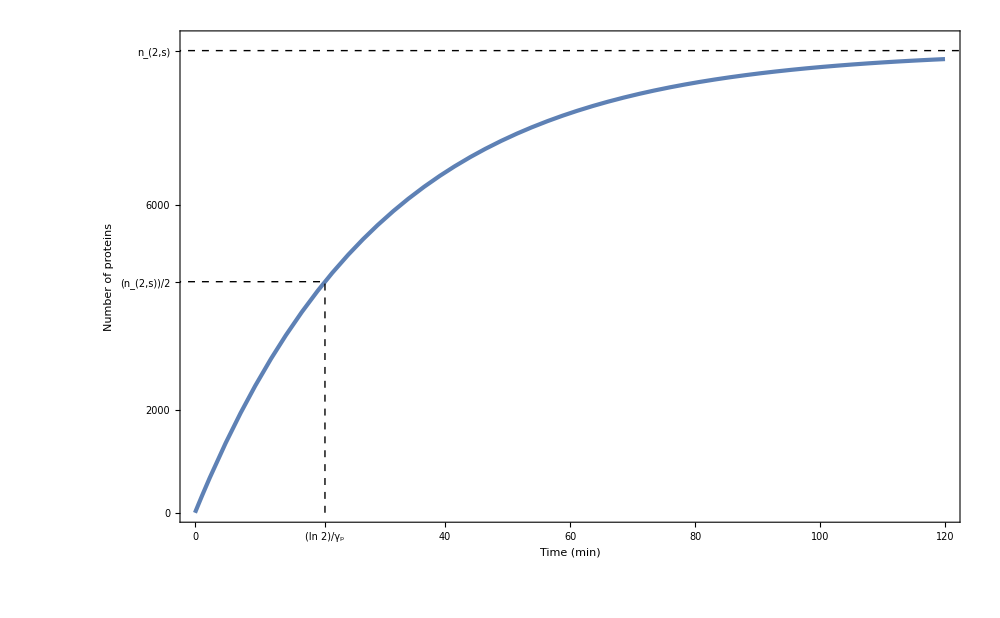

```mathematica
kr=1;
kp=60;
gr=1/5;
gp=1/30;
n1s = kr/gr;
n2[t_]:=kp/gp*n1s*(1-Exp[-gp t]);
optGen={Axes->None,Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->AbsoluteThickness[3],LabelStyle->Directive[30,FontFamily->"Palatino Linotype",Black],FrameLabel->{Text[Style["Time (min)"]],Text[Style["Number of proteins"]]},PlotRange->{0,9200}};
imSize = {ImageSize->1000};
addLineTh= {Epilog->{Directive[Black,Dashed,Thick],{Line[{{-10,n2[Log[2]/gp]},{Log[2]/gp,n2[Log[2]/gp]}}],Line[{{Log[2]/gp,0},{Log[2]/gp,n2[Log[2]/gp]}}],Line[{{-10,kp/gp*n1s},{10/gp,kp/gp*n1s}}]}}};
ticksSetIn = {30,Black,FontFamily->"Palatino Linotype"};
ticks=FrameTicks->{{{0,2000,{0.5*kp/gp*n1s,Style[ToExpression["\\frac{n_{2,s}}{2}",TeXForm,HoldForm],Evaluate[ticksSetIn]]},6000,{kp/gp*n1s,Style[ToExpression["n_{2,s}",TeXForm,HoldForm],Evaluate[ticksSetIn]]}},None},{{0,{Log[2]/gp,Style[ToExpression["\\frac{\\ln 2}{\\gamma_p}",TeXForm,HoldForm],Evaluate[ticksSetIn]]},40,60,80,100,120},None}};

Gexp=Show[Plot[n2[t],{t,0,4/gp},Evaluate[optGen]],Evaluate[imSize],Evaluate[addLineTh],Evaluate[ticks]]
Export["/home/gutiloluis/61Monograph/images/mas-detSol.png",Gexp];
```

```mathematica
FrameTicks->{{Automatic,None},{{0,{1.5,Style["P1\n1.5",Red,14]},2,4,6,{7,Style["P2\n7.0",Red,14]},8,10},None}},
```